```mathematica
(* 1 = linear (for upper-right quad)  2 = parabolic  3 = Harris-like *)
(* 3 doesn't integrate analytically *)
whichprofile=2;
```

```mathematica
Clear[uxin,d,L,uyin,uyout,y,x,uxcorner,uycorner,Bzcorner,Bxcorner,Bycorner,rhocorner,pcorner,xp,yp]
```

```mathematica
simples={Im[1/uxin]==0,Im[uxin]==0,d>0,L>0,Im[1/uyin]==0,Im[uyin]==0,Im[1/uyout]==0,Im[uyout]==0,Im[y]==0,Im[x]==0,Im[uxcorner]==0,Im[uycorner]==0,Im[Bzcorner]==0,Im[Bxcorner]==0,Im[Bycorner]==0,Im[rhocorner]==0,Im[pcorner]==0,x>0,y>0,xp>0,yp>0,z0>0}
```

{Im[1/uxin]==0,Im[uxin]==0,d>0,L>0,Im[1/uyin]==0,Im[uyin]==0,Im[1/uyout]==0,Im[uyout]==0,Im[y]==0,Im[x]==0,Im[uxin]==0,Im[uyout]==0,Im[Bzin]==0,Im[Bxout]==0,Im[Byin]==0,Im[rhoin]==0,Im[pin]==0,x>0,y>0,xp>0,yp>0,z0>0}

```mathematica
If[whichprofile==1,
Az=-Byin*(x/2)*(x/d)+Bxout*(y/2)*(y/L);
]

(*
Bxfake=Bxout*(y/L)*(1-x/d)+Bxcorner*(y/L)*(x/d)
Byfake=Byin*(x/d)*(1-y/L)+Bycorner*(y/L)*(x/d)
one=Integrate[Bxfake,y]
two=Integrate[-Byfake,x]
total=FullSimplify[one+two]
*)
If[whichprofile==2,
Clera[CC,DD,EE,FF,x,y];
total=CC*(x/d)^2+DD*(y/L)^2+EE*(x/d)^2*Sqrt[(y/L)^2]+FF*(y/L)^2*Sqrt[(x/d)^2];
Bx=FullSimplify[D[total,y]];
By=FullSimplify[-D[total,x]];
eq1=FullSimplify[Byin-(By//.{x->d,y->0})];
eq2=FullSimplify[Bycorner-(By//.{x->d,y->L})];
eq3=FullSimplify[Bxout-(Bx//.{x->0,y->L})];
eq4=FullSimplify[Bxcorner-(Bx//.{x->d,y->L})];
sols=Solve[{eq1==0,eq2==0,eq3==0,eq4==0},{CC,DD,EE,FF}];
Az=FullSimplify[total//.sols[[1]]];
collectedAz=Collect[Az,{x,y}];
Print[collectedAz];
]

If[whichprofile==3,
(*
(* ok, but doesn't allow corner values *)
Clear[AA,BB,d,L,Byin,Bxout];
fun=AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]];
eq1=Byin==(-D[fun,x]//.{x->d,y->0});
eq2=Bxout==(D[fun,y]//.{x->0,y->L});
solsfun=Solve[{eq1,eq2},{AA,BB}];
Az=fun//.solsfun[[1]];
*)
(*
(* uses spherical cosh to reach constant field strength beyind current sheet -- could use Gaussian *)
(* but uses twice layer size to get freedom *)
Clear[AA,BB,CC,DD,x,y,d,L];
fun=(AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]]+CC*Log[Cosh[x/(2*d)]]+DD*Log[Cosh[y/(2*L)]])*(Cosh[Sqrt[(x/d)^2+(y/L)^2]])^(-2);
eq1=Byin==(-D[fun,x]//.{x->d,y->0});
eq2=Bxout==(D[fun,y]//.{x->0,y->L});
eq3=Bycorner==(-D[fun,x]//.{x->d,y->L});
eq4=Bxcorner==(D[fun,y]//.{x->d,y->L});
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}];
Az=fun//.solsfun[[1]];
*)

(* uses spherical cosh for large radius suppression, and also only uses d and L lengths *)
fun=AA*Log[Cosh[x/d]]+(BB*Log[Cosh[y/L]]+CC*(Log[Cosh[x/d]]+Sech[x/d]^2/2)+DD*(Log[Cosh[y/L]]+Sech[y/L]^2/2))*(Cosh[Sqrt[(x/d)^2+(y/L)^2]])^(-2);
(*fun=AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]]+CC*Log[Cosh[x/(d)]^2]+DD*Log[Cosh[y/(L)]^2];*)
eq1=Byin==(-D[fun,x]//.{x->d,y->0});
eq2=Bxout==(D[fun,y]//.{x->0,y->L});
eq3=Bycorner==(-D[fun,x]//.{x->d,y->L});
eq4=Bxcorner==(D[fun,y]//.{x->d,y->L});
solsfun3=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}];
Az=fun//.solsfun3[[1]];

]
```

1/6 ((3 Bxout)/L+(2 Bycorner d √(x^2/d^2))/L^2-(2 Byin d √(x^2/d^2))/L^2+(4 Bxcorner √(x^2/d^2))/L-(4 Bxout √(x^2/d^2))/L) y^2+1/6 x^2 (-(3 Byin)/d-(4 Bycorner √(y^2/L^2))/d+(4 Byin √(y^2/L^2))/d-(2 Bxcorner L √(y^2/L^2))/d^2+(2 Bxout L √(y^2/L^2))/d^2)

{L→10,d→1,Byin→1,Bxout→0.1,Bycorner→0.8,Bxcorner→0.05}

1/6 (-3 x^2+0.03 y^2-0.024 √(x^2) y^2+0.18 x^2 √(y^2))

-x^2/2+0.005 y^2

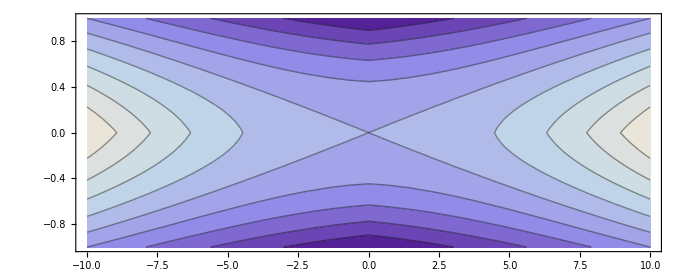

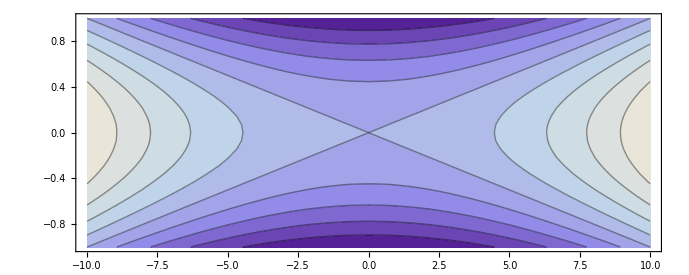

```mathematica
consts={L->10,d->1,Byin->1,Bxout->0.1,Bycorner->0.8,Bxcorner->0.05}
(*consts={L->10,d->1,Byin->1,Bxout->0.1,Bycorner->Byin,Bxcorner->Bxout}*)
toplot=Az//.consts
Azorig=-Byin*(x/2)*(x/d)+Bxout*(y/2)*(y/L);
toplot2=Azorig//.consts
ContourPlot[toplot,{y,-10,10},{x,-1,1},AspectRatio->Automatic]
ContourPlot[toplot2,{y,-10,10},{x,-1,1},AspectRatio->Automatic]
```

```mathematica
(* Set stuff *)

uz=0;

(*
ux=x/d*uxin
uy=y/L*uyin
*)
(* ONLY FOR upper-right quarter area *)
If[whichprofile==1 || whichprofile==2,
ux=uxin*(x/d)*(1-(y/L)) + uxcorner*(x/d)*(y/L);
uy=uyout*(1-x/d)*(y/L) + uycorner*(x/d)*(y/L);
]
If[whichprofile==3,
(*
(* bad behavior since not localized *)
fun=AA*(x/d)*Cosh[x/d]^(-2);
eq1=uxin==(fun//.{x->d,y->0});
solsfun=Solve[eq1,AA];
ux=fun//.solsfun[[1]];

fun=AA*(y/L)*Cosh[y/L]^(-2);
eq1=uyout==(fun//.{x->0,y->L});
solsfun=Solve[eq1,AA];
uy=fun//.solsfun[[1]];
*)

(*
(* other type of extended cosh profile *)
fun=AA*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-2)+BB*(x/d)*Cosh[x/d]^(-2)*Cosh[y/(2*L)]^(-2)
eq1=uxin==(fun//.{x->d,y->0})
eq2=uxcorner==(fun//.{x->d,y->L})
solsfun=Solve[{eq1,eq2},{AA,BB}]
ux=fun//.solsfun
*)
(*
(* localized extended cosh profile with d and L as still characteristic lengths*)
fun=AA*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-2)+BB*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-4);
eq1=uxin==(fun//.{x->d,y->0});
eq2=uxcorner==(fun//.{x->d,y->L});
solsfun=Solve[{eq1,eq2},{AA,BB}];
ux=fun//.solsfun;

fun=AA*(y/L)*Cosh[x/d]^(-2)*Cosh[y/L]^(-2)+BB*(y/L)*Cosh[x/d]^(-4)*Cosh[y/L]^(-2);
eq1=uyout==(fun//.{x->0,y->L});
eq2=uycorner==(fun//.{x->d,y->L});
solsfun=Solve[{eq1,eq2},{AA,BB}];
uy=fun//.solsfun;
*)

(* uses d and L, but less order for suppression term *)
fun=AA*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-1)+BB*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-2);
eq1=uxin==(fun//.{x->d,y->0});
eq2=uxcorner==(fun//.{x->d,y->L});
solsfun=Solve[{eq1,eq2},{AA,BB}];
ux=fun//.solsfun;

fun=AA*(y/L)*Cosh[y/L]^(-2)*Cosh[x/d]^(-1)+BB*(y/L)*Cosh[y/L]^(-2)*Cosh[x/d]^(-2);
eq1=uyout==(fun//.{x->0,y->L});
eq2=uycorner==(fun//.{x->d,y->L});
solsfun=Solve[{eq1,eq2},{AA,BB}];
uy=fun//.solsfun;
]

If[whichprofile==2,
Bz=Bzc*(1-(x/d)^2)*(1-(y/L)^2)+Bzin*(x/d)^2*(1-(y/L)^2)+Bzout*(1-(x/d)^2)*(y/L)^2+Bzcorner*(x/d)^2*(y/L)^2;
rho=rhoc*(1-(x/d)^2)*(1-(y/L)^2)+rhoin*(x/d)^2*(1-(y/L)^2)+rhoout*(1-(x/d)^2)*(y/L)^2+rhocorner*(x/d)^2*(y/L)^2;
p=pc*(1-(x/d)^2)*(1-(y/L)^2)+pin*(x/d)^2*(1-(y/L)^2)+pout*(1-(x/d)^2)*(y/L)^2+pcorner*(x/d)^2*(y/L)^2;
]
(* ONLY FOR upper-right quarter area *)
If[whichprofile==1,
Bz=Bzc*(1-(x/d)^1)*(1-(y/L)^1)+Bzin*(x/d)^1*(1-(y/L)^1)+Bzout*(1-(x/d)^1)*(y/L)^1+Bzcorner*(x/d)^1*(y/L)^1;
rho=rhoc*(1-(x/d)^1)*(1-(y/L)^1)+rhoin*(x/d)^1*(1-(y/L)^1)+rhoout*(1-(x/d)^1)*(y/L)^1+rhocorner*(x/d)^1*(y/L)^1;
p=pc*(1-(x/d)^1)*(1-(y/L)^1)+pin*(x/d)^1*(1-(y/L)^1)+pout*(1-(x/d)^1)*(y/L)^1+pcorner*(x/d)^1*(y/L)^1;
]
If[whichprofile==3,
(*
(* not monotonic *)
fun=AA+BB*Cosh[y/L]^(-2)+CC*Cosh[x/d]^(-2);

eq1=Bzc==(fun//.{y->0,x->0});
eq2=Bzin==(fun//.{y->0,x->d});
eq3=Bzout==(fun//.{y->L,x->0});
solsfun=Solve[{eq1,eq2,eq3},{AA,BB,CC}];
Bz=fun//.solsfun[[1]];

eq1=rhoc==(fun//.{y->0,x->0});
eq2=rhoin==(fun//.{y->0,x->d});
eq3=rhoout==(fun//.{y->L,x->0});
solsfun=Solve[{eq1,eq2,eq3},{AA,BB,CC}];
rho=fun//.solsfun[[1]];

eq1=pc==(fun//.{y->0,x->0});
eq2=pin==(fun//.{y->0,x->d});
eq3=pout==(fun//.{y->L,x->0});
solsfun=Solve[{eq1,eq2,eq3},{AA,BB,CC}];
p=fun//.solsfun[[1]];
*)

fun=AA+BB*Cosh[Sqrt[(x/d)^2+(y/L)^2]]^(-2)+CC*Cosh[Sqrt[(x/d)^2+(y/(2*L))^2]]^(-2)+DD*Cosh[Sqrt[(x/(2*d))^2+(y/L)^2]]^(-2);

eq1=Bzc==(fun//.{y->0,x->0});
eq2=Bzin==(fun//.{y->0,x->d});
eq3=Bzout==(fun//.{y->L,x->0});
eq4=Bzcorner==(fun//.{y->L,x->d});
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}];
whichsol=1;
Bz=fun//.solsfun[[whichsol]];

eq1=rhoc==(fun//.{y->0,x->0});
eq2=rhoin==(fun//.{y->0,x->d});
eq3=rhoout==(fun//.{y->L,x->0});
eq4=rhocorner==(fun//.{y->L,x->d});
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}];
whichsol=1;
rho=fun//.solsfun[[whichsol]];

eq1=pc==(fun//.{y->0,x->0});
eq2=pin==(fun//.{y->0,x->d});
eq3=pout==(fun//.{y->L,x->0});
eq4=pcorner==(fun//.{y->L,x->d});
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}];
whichsol=1;
p=fun//.solsfun[[whichsol]];
]


(* have to choose else too complicated for mathematica to integrate *)
Clear[x,y,Bxcorner,Bycorner,Bzcorner,rhocorner,pcorner,uxcorner,uycorner]

Bxcorner=Bxout
Bycorner=Byin

Bzcorner=(Bzin+Bzout)/2
rhocorner=(rhoin+rhoout)/2
pcorner=(pin+pout)/2

uxcorner=uxin
uycorner=uyout

Az=FullSimplify[Az,simples];
rho=FullSimplify[rho,simples];
Bz=FullSimplify[Bz,simples];
p=FullSimplify[p,simples];
ux=FullSimplify[ux,simples];
uy=FullSimplify[uy,simples];

(* computations, not setup *)

gamma=Sqrt[1+ux^2+uy^2+uz^2]
ut=gamma

Bx=FullSimplify[D[Az,y],simples];
By=FullSimplify[-D[Az,x],simples];


u=p/(Gam-1)
udotB=ux*Bx+uy*By+uz*Bz
(* only in ideal MHD *)
bt=udotB
bx=(Bx+udotB*ux)/gamma
by=(By+udotB*uy)/gamma
bz=(Bz+udotB*uz)/gamma

bsq=bt^2+bx^2+by^2+bz^2

(* only in ideal MHD *)
Txx=(rho+u+p+bsq)*ux*ux+(p+bsq/2)-bx*bx
Tyy=(rho+u+p+bsq)*uy*uy+(p+bsq/2)-by*by
Tyx=(rho+u+p+bsq)*uy*ux-by*bx
Txz=(rho+u+p+bsq)*ux*uz-bx*bz
Tyz=(rho+u+p+bsq)*uy*uz-by*bz
Ttx=(rho+u+p+bsq)*ut*ux-bt*bx
Tty=(rho+u+p+bsq)*ut*uy-bt*by
```

Bxout

Byin

(Bzin+Bzout)/2

(rhoin+rhoout)/2

(pin+pout)/2

uxin

uyout

√(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)

√(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)

(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 (-1+Gam) L^2)

(Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)

(Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)

((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)/(√(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))

((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)/(√(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))

(2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))/(2 d^2 L^2 √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))

((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L))^2+((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))^2)/(4 d^4 L^4 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))

-((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 L^2)+1/2 (((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L))^2+((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))^2)/(4 d^4 L^4 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)))+1/d^2 uxin^2 x^2 (((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L))^2+((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))^2)/(4 d^4 L^4 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 L^2)+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 (-1+Gam) L^2)+(2 d^2 (L^2 rhoc+(-rhoc+rhoout) y^2)-x^2 (2 L^2 (rhoc-rhoin)+(-2 rhoc+rhoin+rhoout) y^2))/(2 d^2 L^2))

-((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 L^2)+1/2 (((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L))^2+((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))^2)/(4 d^4 L^4 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)))+1/L^2 uyout^2 y^2 (((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L))^2+((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))^2)/(4 d^4 L^4 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 L^2)+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 (-1+Gam) L^2)+(2 d^2 (L^2 rhoc+(-rhoc+rhoout) y^2)-x^2 (2 L^2 (rhoc-rhoin)+(-2 rhoc+rhoin+rhoout) y^2))/(2 d^2 L^2))

-(((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d) ((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L))/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+1/(d L)uxin uyout x y (((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L))^2+((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))^2)/(4 d^4 L^4 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 L^2)+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 (-1+Gam) L^2)+(2 d^2 (L^2 rhoc+(-rhoc+rhoout) y^2)-x^2 (2 L^2 (rhoc-rhoin)+(-2 rhoc+rhoin+rhoout) y^2))/(2 d^2 L^2))

-1/(2 d^2 L^2 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d) (2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))

-1/(2 d^2 L^2 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L) (2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))

-(((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)) ((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d))/(√(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))+1/d uxin x √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2) (((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L))^2+((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))^2)/(4 d^4 L^4 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 L^2)+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 (-1+Gam) L^2)+(2 d^2 (L^2 rhoc+(-rhoc+rhoout) y^2)-x^2 (2 L^2 (rhoc-rhoin)+(-2 rhoc+rhoin+rhoout) y^2))/(2 d^2 L^2))

-(((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)) ((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L))/(√(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))+1/L uyout y √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2) (((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L))^2+((Bxout y)/L+(uxin x ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/d)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((Byin x)/d+(uyout y ((Bxout uxin x y)/(d L)+(Byin uyout x y)/(d L)))/L)^2/(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)+((2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))^2)/(4 d^4 L^4 (1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 L^2)+(2 d^2 (L^2 pc+(-pc+pout) y^2)-x^2 (2 L^2 (pc-pin)+(-2 pc+pin+pout) y^2))/(2 d^2 (-1+Gam) L^2)+(2 d^2 (L^2 rhoc+(-rhoc+rhoout) y^2)-x^2 (2 L^2 (rhoc-rhoin)+(-2 rhoc+rhoin+rhoout) y^2))/(2 d^2 L^2))

```mathematica
FullSimplify[Byin-(By//.{x->d,y->0})]
FullSimplify[Bycorner-(By//.{x->d,y->L})]
FullSimplify[Bxout-(Bx//.{x->0,y->L})]
FullSimplify[Bxcorner-(Bx//.{x->d,y->L})]
```

0

0

0

«1 more identical outputs»

```mathematica
uxin-(ux//.{x->d,y->0})
uxcorner-(ux//.{x->d,y->L})
uyout-(uy//.{x->0,y->L})
uycorner-(uy//.{x->d,y->L})
```

0

0

0

«1 more identical outputs»

```mathematica
jonintegratex[inputfun0_,simples0_]:=
Module[{foo,ii,numterms,resultterm,simples=simples0,inputfun=inputfun0,outputfun},
outputfun=0;
inputfunnew=inputfun//.{y->yp*L,x->xp*d};
numterms=Dimensions[Expand[inputfunnew]][[1]];
For[ii=1,ii<=numterms,ii++,
resultterm=Integrate[Expand[inputfunnew][[ii]],{xp,0,1},Assumptions->simples];
Print[ii," of ",numterms];
Print[resultterm];
outputfun=outputfun+resultterm;
];
(* send back result *)
outputfun//.{xp->x/d,yp->y/L}
];
```

```mathematica
(* at y=0 from x=0 to x=d *)
Txxhere=Txx;
Tyxhere=Tyx;
Print["Integrating a"];
(* resulta has no rhoc *)
(*resulta=Integrate[D[Txxhere,x],{x,0,d},Assumptions->simples];*)
resulta=((Txxhere//.{x->d})-(Txxhere//.{x->0}))//.{y->0};
Print["Simples b"];
resultb0=Simplify[(D[Tyxhere,y])//.{y->0},simples];
Print["Integrating b"];
(* resultb still depends upon rhoc because v^i is linear and term is rhoc*x*y that leads to rhoc d^2 *)
(* if velocity was ux=x^2 and ux=y^2, then wouldn't happen, or ux=x^3 and uy=y^3, but higher order than expected *)
resultb=Integrate[resultb0,{x,0,d},Assumptions->simples];
result=resulta+resultb;
Print["Simplifying"];
result1=Simplify[result,simples]
```

Integrating a

Simples b

Integrating b

Simplifying

1/4 (-2 Bzc^2-4 pc+4 pin+(2 (Byin^2+Bzin^2))/(1+uxin^2)+(4 uxin^2 (Byin^2 (-1+Gam)+Bzin^2 (-1+Gam)+(-rhoin+Gam (pin+rhoin)) (1+uxin^2)))/((-1+Gam) (1+uxin^2))+1/((-1+Gam) L uxin^5)d (uxin^2 (-2 Bxout Byin (-1+Gam) uxin^3+((-rhoc-rhoin+Gam (pc+pin+rhoc+rhoin)) uxin^4+Bzin^2 (-1+Gam) (-2+uxin^2)+2 Bzc Bzin (-1+Gam) (2+uxin^2)-Bzc^2 (-1+Gam) (2+3 uxin^2)) uyout)-4 (-1+Gam) (Bzc-Bzin+Bzc uxin^2)^2 uyout Log[d]+2 (-1+Gam) (Bzc-Bzin+Bzc uxin^2)^2 uyout Log[d^2 (1+uxin^2)]))

```mathematica
testsimplify1=FullSimplify[result1//.{pc->totalpc-Bzc^2/2},simples]
```

1/4 (-2 Bzc^2+4 pin+2 (Bzc^2-2 totalpc)+(2 (Byin^2+Bzin^2))/(1+uxin^2)+4 uxin^2 ((Gam pin)/(-1+Gam)+rhoin+(Byin^2+Bzin^2)/(1+uxin^2))+1/(2 (-1+Gam) L uxin^5)d (-4 Bxout Byin (-1+Gam) uxin^5+uxin^2 (-4 (Bzc-Bzin)^2 (-1+Gam)-2 (Bzc-Bzin) (3 Bzc+Bzin) (-1+Gam) uxin^2+(-2 (rhoc+rhoin)+Gam (-Bzc^2+2 (pin+rhoc+rhoin+totalpc))) uxin^4) uyout+4 (-1+Gam) (Bzc-Bzin+Bzc uxin^2)^2 uyout Log[1+uxin^2]))

```mathematica
(* at x=0 from y=0 to x=L *)
Tyyhere=Tyy;
Tyxhere=Tyx;
resulta=((Tyyhere//.{y->L})-(Tyyhere//.{y->0}))//.{x->0};
resultb0=Simplify[(D[Tyxhere,x])//.{x->0},simples];
resultb=Integrate[resultb0,{y,0,L},Assumptions->simples];
(*result=Integrate[D[Tyyhere,y]+D[Tyxhere,x],{y,0,L},Assumptions->simples];*)
result=resulta+resultb;
result2=Simplify[result,simples]
```

1/4 (-2 Bzc^2-4 pc+4 pout+(2 (Bxout^2+Bzout^2))/(1+uyout^2)+(4 uyout^2 (Bxout^2 (-1+Gam)+Bzout^2 (-1+Gam)+(-rhoout+Gam (pout+rhoout)) (1+uyout^2)))/((-1+Gam) (1+uyout^2))+1/(d (-1+Gam) uyout^5)L (uyout^2 (uyout^3 (-2 Bxout Byin (-1+Gam)+(-rhoc-rhoout+Gam (pc+pout+rhoc+rhoout)) uxin uyout)+Bzout^2 (-1+Gam) uxin (-2+uyout^2)+2 Bzc Bzout (-1+Gam) uxin (2+uyout^2)-Bzc^2 (-1+Gam) uxin (2+3 uyout^2))-4 (-1+Gam) uxin (Bzc-Bzout+Bzc uyout^2)^2 Log[L]+2 (-1+Gam) uxin (Bzc-Bzout+Bzc uyout^2)^2 Log[L^2 (1+uyout^2)]))

```mathematica
testsimplify2=FullSimplify[result2//.{pc->totalpc-Bzc^2/2},simples]
```

1/4 (4 Bxout^2-(2 Bxout Byin L)/d+4 (Bzout^2+pout-totalpc)-(2 (Bzc-Bzout)^2 L uxin)/(d uyout^3)+((-Bzc+Bzout) (3 Bzc+Bzout) L uxin)/(d uyout)+(L (-2 (rhoc+rhoout)+Gam (-Bzc^2+2 (pout+rhoc+rhoout+totalpc))) uxin uyout)/(2 d (-1+Gam))+(4 (-rhoout+Gam (pout+rhoout)) uyout^2)/(-1+Gam)-(2 (Bxout^2+Bzout^2))/(1+uyout^2)+(2 L uxin (Bzc-Bzout+Bzc uyout^2)^2 Log[1+uyout^2])/(d uyout^5))

```mathematica
(* at y=0 from x=0 to x=d *)
Txzhere=Txz;
Tyzhere=Tyz;
Print["Integrating a"];
(*result=Integrate[D[Txzhere,x]+D[Tyzhere,y],{x,0,d},Assumptions->simples];*)
resulta=((Txzhere//.{x->d})-(Txzhere//.{x->0}))//.{y->0};
Print["Simples b"];
resultb0=Simplify[(D[Tyzhere,y])//.{y->0},simples];
Print["Integrating b"];
resultb=Integrate[resultb0,{x,0,d},Assumptions->simples];
result=resulta+resultb;
Print["Simplifying"];
result3=Simplify[result,simples]
```

Integrating a

Simples b

Integrating b

Simplifying

0

```mathematica
(* at x=0 from y=0 to x=L *)
Txzhere=Txz;
Tyzhere=Tyz;
(*result=Integrate[D[Tyzhere,y]+D[Txzhere,x],{y,0,L},Assumptions->simples];*)
resulta=((Tyzhere//.{y->L})-(Tyzhere//.{y->0}))//.{x->0};
resultb0=Simplify[(D[Txzhere,x])//.{x->0},simples];
resultb=Integrate[resultb0,{y,0,L},Assumptions->simples];
(*result=Integrate[D[Tyyhere,y]+D[Tyxhere,x],{y,0,L},Assumptions->simples];*)
result=resulta+resultb;
result4=Simplify[result,simples]
```

0

```mathematica
(* volume integration -- doesn't depend upon rhoc for whichproblem==2 -- because v=0 at center *)
rhouxXU=rho*ux//.{x->d};
rhouxXD=rho*ux//.{x->0};
Drhoux=rhouxXU-rhouxXD;
rhouyYU=rho*uy//.{y->L};
rhouyYD=rho*uy//.{y->0};
Drhouy=rhouyYU-rhouyYD;
result=Integrate[Drhoux,{y,0,L},Assumptions->simples]+Integrate[Drhouy,{x,0,d},Assumptions->simples];
result5=Simplify[result,simples]
```

1/6 (L (5 rhoin+rhoout) uxin+d (rhoin+5 rhoout) uyout)

```mathematica
(* volume integration -- doesn't depend upon rhoc,Bzc,pc for whichproblem==2 -- because v=0 at center and center quantities don't enter at all at other locations *)
TtxXU=Ttx//.{x->d};
TtxXD=Ttx//.{x->0};
DTtx=TtxXU-TtxXD;
TtyYU=Tty//.{y->L};
TtyYD=Tty//.{y->0};
DTty=TtyYU-TtyYD;
result=Integrate[DTtx,{y,0,L},Assumptions->simples]+Integrate[DTty,{x,0,d},Assumptions->simples];
(* corner density is same as inflow density *)
result6=Simplify[result,simples]
Simplify[result6-(result6//.{rhoc->0}),simples]
Simplify[result6-(result6//.{Bzc->0}),simples]
Simplify[result6-(result6//.{pc->0}),simples]
```

1/(32 (-1+Gam))(d ((32 Bxout^2 (-1+Gam) uyout ArcSinh[Abs[uxin]/(√(1+uyout^2))])/Abs[uxin]+(32 Bzout^2 (-1+Gam) uyout ArcSinh[Abs[uxin]/(√(1+uyout^2))])/Abs[uxin]+(32 (-rhoout+Gam (pout+rhoout)) uyout (1+uyout^2) ArcSinh[Abs[uxin]/(√(1+uyout^2))])/Abs[uxin]-(16 Bzin Bzout (-1+Gam) uyout (-uxin^2 √(1+uxin^2+uyout^2)+(1+uyout^2) Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))]))/uxin^4+(16 Bzout^2 (-1+Gam) uyout (-uxin^2 √(1+uxin^2+uyout^2)+(1+uyout^2) Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))]))/uxin^4-(32 Bxout^2 (-1+Gam) uyout (1+uyout^2) (-uxin^2 √(1+uxin^2+uyout^2)+(1+uyout^2) Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))]))/uxin^2-1/uxin^3 16 Bxout Byin (-1+Gam) (-1+4 uyout^2+4 uyout^4) (-uxin^2 √(1+uxin^2+uyout^2)+(1+uyout^2) Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))])-1/uxin^4 8 uyout (rhoout-2 rhoout uxin^2-4 Byin^2 uyout^2+rhoout uyout^2-4 Byin^2 uyout^4-rhoin (1+uyout^2)+Gam (pin-pout+rhoin-rhoout+2 pout uxin^2+2 rhoout uxin^2+4 Byin^2 uyout^2+pin uyout^2-pout uyout^2+rhoin uyout^2-rhoout uyout^2+4 Byin^2 uyout^4)) (-uxin^2 √(1+uxin^2+uyout^2)+(1+uyout^2) Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))])-1/uxin^6 2 Bzin Bzout (-1+Gam) uyout (uxin^2 √(1+uxin^2+uyout^2) (2 uxin^2-3 (1+uyout^2))+3 (1+uyout^2)^2 Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))])+1/uxin^6 Bzout^2 (-1+Gam) uyout (uxin^2 √(1+uxin^2+uyout^2) (2 uxin^2-3 (1+uyout^2))+3 (1+uyout^2)^2 Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))])+1/uxin^2 8 Bxout^2 (-1+Gam) uyout (uxin^2 √(1+uxin^2+uyout^2) (2 uxin^2-3 (1+uyout^2))+3 (1+uyout^2)^2 Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))])+1/uxin^3 16 Bxout Byin (-1+Gam) uyout^2 (uxin^2 √(1+uxin^2+uyout^2) (2 uxin^2-3 (1+uyout^2))+3 (1+uyout^2)^2 Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))])+1/uxin^6 uyout (Bzin^2 (-1+Gam)+2 uxin^2 (-rhoin+rhoout-4 Byin^2 uyout^2+Gam (pin-pout+rhoin-rhoout+4 Byin^2 uyout^2))) (uxin^2 √(1+uxin^2+uyout^2) (2 uxin^2-3 (1+uyout^2))+3 (1+uyout^2)^2 Abs[uxin] ArcSinh[Abs[uxin]/(√(1+uyout^2))]))+L ((32 Byin^2 (-1+Gam) uxin ArcSinh[Abs[uyout]/(√(1+uxin^2))])/Abs[uyout]+(32 Bzin^2 (-1+Gam) uxin ArcSinh[Abs[uyout]/(√(1+uxin^2))])/Abs[uyout]-(32 rhoin uxin ArcSinh[Abs[uyout]/(√(1+uxin^2))])/Abs[uyout]-(32 rhoin uxin^3 ArcSinh[Abs[uyout]/(√(1+uxin^2))])/Abs[uyout]+(32 Gam (pin+rhoin) uxin (1+uxin^2) ArcSinh[Abs[uyout]/(√(1+uxin^2))])/Abs[uyout]+(16 Bzin^2 (-1+Gam) uxin (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4-(16 Bzin Bzout (-1+Gam) uxin (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4-(8 rhoin uxin (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4+(8 rhoout uxin (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4+(32 Bxout^2 uxin^3 (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4-(8 rhoin uxin^3 (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4+(8 rhoout uxin^3 (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4+(32 Bxout^2 uxin^5 (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4-1/uyout^3 16 Bxout Byin (-1+Gam) (-1+4 uxin^2+4 uxin^4) (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))])+(16 rhoin uxin (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^2-(32 Byin^2 (-1+Gam) uxin (1+uxin^2) (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^2-1/uyout^4 8 Gam uxin (pout-rhoin+rhoout+4 Bxout^2 uxin^2+pout uxin^2-rhoin uxin^2+rhoout uxin^2+4 Bxout^2 uxin^4+2 rhoin uyout^2-pin (1+uxin^2-2 uyout^2)) (-uyout^2 √(1+uxin^2+uyout^2)+(1+uxin^2) Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))])-(Bzout^2 uxin (uyout^2 √(1+uxin^2+uyout^2) (-3-3 uxin^2+2 uyout^2)+3 (1+uxin^2)^2 Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^6+1/uyout^6 Bzin^2 (-1+Gam) uxin (uyout^2 √(1+uxin^2+uyout^2) (-3-3 uxin^2+2 uyout^2)+3 (1+uxin^2)^2 Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))])-1/uyout^6 2 Bzin Bzout (-1+Gam) uxin (uyout^2 √(1+uxin^2+uyout^2) (-3-3 uxin^2+2 uyout^2)+3 (1+uxin^2)^2 Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))])+(2 rhoin uxin (uyout^2 √(1+uxin^2+uyout^2) (-3-3 uxin^2+2 uyout^2)+3 (1+uxin^2)^2 Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4-(2 rhoout uxin (uyout^2 √(1+uxin^2+uyout^2) (-3-3 uxin^2+2 uyout^2)+3 (1+uxin^2)^2 Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4-(8 Bxout^2 uxin^3 (uyout^2 √(1+uxin^2+uyout^2) (-3-3 uxin^2+2 uyout^2)+3 (1+uxin^2)^2 Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))]))/uyout^4+1/uyout^3 16 Bxout Byin (-1+Gam) uxin^2 (uyout^2 √(1+uxin^2+uyout^2) (-3-3 uxin^2+2 uyout^2)+3 (1+uxin^2)^2 Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))])+1/uyout^2 8 Byin^2 (-1+Gam) uxin (uyout^2 √(1+uxin^2+uyout^2) (-3-3 uxin^2+2 uyout^2)+3 (1+uxin^2)^2 Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))])+1/uyout^6 Gam uxin (Bzout^2+2 (-pin+pout-rhoin+rhoout+4 Bxout^2 uxin^2) uyout^2) (uyout^2 √(1+uxin^2+uyout^2) (-3-3 uxin^2+2 uyout^2)+3 (1+uxin^2)^2 Abs[uyout] ArcSinh[Abs[uyout]/(√(1+uxin^2))])))

```mathematica
(* didn't complete this full simplify *)
(*testsimplify6=FullSimplify[result6//.{pc->totalpc-Bzc^2/2},simples]*)
```

```mathematica
(* Ez = constant *)
vx=ux/gamma
vy=uy/gamma
vz=uz/gamma
Ez=-vx*By+vy*Bx
EzA = Ez*d*L (* assumes Ez is constant,which it will be *)
EzA = Integrate[Ez,{x,0,d},{y,0,L},Assumptions->simples]
EzA1=EzA//.{x->0,y->L}
EzA2=EzA//.{x->d,y->0}
```

(uxin x)/(d √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))

(uyout y)/(L √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))

0

-(Byin uxin x^2)/(d^2 √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))+(Bxout uyout y^2)/(L^2 √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))

d L (-(Byin uxin x^2)/(d^2 √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))+(Bxout uyout y^2)/(L^2 √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2)))

(Bxout d L (uxin √(1+uxin^2+uyout^2)+(1+uyout^2) ArcSinh[uxin/(√(1+uyout^2))]))/(4 uxin uyout)-1/(4 uxin uyout^2)Bxout d L (2 uxin ArcSinh[uyout/(√(1+uxin^2))]-2 ArcTan[(uxin uyout)/(√(1+uxin^2+uyout^2))]-uyout Log[1+uyout^2]+2 uyout Log[uxin+√(1+uxin^2+uyout^2)])-(Bxout d L (4 uxin^3 √(1+uxin^2+uyout^2) ArcSinh[uyout/(√(1+uxin^2))]+4 √(1+uxin^2+uyout^2) ArcTan[(uxin uyout)/(√(1+uxin^2+uyout^2))]+uyout ((3+uyout^2) √(1+uxin^2+uyout^2) Log[1+uyout^2]+2 (uxin (1+uxin^2+uyout^2)-(3+uyout^2) √(1+uxin^2+uyout^2) Log[uxin+√(1+uxin^2+uyout^2)]))))/(24 uxin uyout^2 √(1+uxin^2+uyout^2))-(Byin d L (2 √(1+uxin^2+uyout^2) (uxin^3 ArcSinh[Abs[uyout]/(√(1+uxin^2))]+ArcTan[(uxin Abs[uyout])/(√(1+uxin^2+uyout^2))])+Abs[uyout] (uxin+uxin^3+uxin uyout^2+uyout^2 √(1+uxin^2+uyout^2) Log[2]+(3+uyout^2) √(1+uxin^2+uyout^2) Log[d uxin √(1+uyout^2)]-3 √(1+uxin^2+uyout^2) Log[d uxin (uxin+√(1+uxin^2+uyout^2))])-√(1+uxin^2+uyout^2) Abs[uyout]^3 Log[2 d uxin (uxin+√(1+uxin^2+uyout^2))]))/(6 uxin^2 √(1+uxin^2+uyout^2) Abs[uyout])

(Bxout d L (uxin √(1+uxin^2+uyout^2)+(1+uyout^2) ArcSinh[uxin/(√(1+uyout^2))]))/(4 uxin uyout)-1/(4 uxin uyout^2)Bxout d L (2 uxin ArcSinh[uyout/(√(1+uxin^2))]-2 ArcTan[(uxin uyout)/(√(1+uxin^2+uyout^2))]-uyout Log[1+uyout^2]+2 uyout Log[uxin+√(1+uxin^2+uyout^2)])-(Bxout d L (4 uxin^3 √(1+uxin^2+uyout^2) ArcSinh[uyout/(√(1+uxin^2))]+4 √(1+uxin^2+uyout^2) ArcTan[(uxin uyout)/(√(1+uxin^2+uyout^2))]+uyout ((3+uyout^2) √(1+uxin^2+uyout^2) Log[1+uyout^2]+2 (uxin (1+uxin^2+uyout^2)-(3+uyout^2) √(1+uxin^2+uyout^2) Log[uxin+√(1+uxin^2+uyout^2)]))))/(24 uxin uyout^2 √(1+uxin^2+uyout^2))-(Byin d L (2 √(1+uxin^2+uyout^2) (uxin^3 ArcSinh[Abs[uyout]/(√(1+uxin^2))]+ArcTan[(uxin Abs[uyout])/(√(1+uxin^2+uyout^2))])+Abs[uyout] (uxin+uxin^3+uxin uyout^2+uyout^2 √(1+uxin^2+uyout^2) Log[2]+(3+uyout^2) √(1+uxin^2+uyout^2) Log[d uxin √(1+uyout^2)]-3 √(1+uxin^2+uyout^2) Log[d uxin (uxin+√(1+uxin^2+uyout^2))])-√(1+uxin^2+uyout^2) Abs[uyout]^3 Log[2 d uxin (uxin+√(1+uxin^2+uyout^2))]))/(6 uxin^2 √(1+uxin^2+uyout^2) Abs[uyout])

(Bxout d L (uxin √(1+uxin^2+uyout^2)+(1+uyout^2) ArcSinh[uxin/(√(1+uyout^2))]))/(4 uxin uyout)-1/(4 uxin uyout^2)Bxout d L (2 uxin ArcSinh[uyout/(√(1+uxin^2))]-2 ArcTan[(uxin uyout)/(√(1+uxin^2+uyout^2))]-uyout Log[1+uyout^2]+2 uyout Log[uxin+√(1+uxin^2+uyout^2)])-(Bxout d L (4 uxin^3 √(1+uxin^2+uyout^2) ArcSinh[uyout/(√(1+uxin^2))]+4 √(1+uxin^2+uyout^2) ArcTan[(uxin uyout)/(√(1+uxin^2+uyout^2))]+uyout ((3+uyout^2) √(1+uxin^2+uyout^2) Log[1+uyout^2]+2 (uxin (1+uxin^2+uyout^2)-(3+uyout^2) √(1+uxin^2+uyout^2) Log[uxin+√(1+uxin^2+uyout^2)]))))/(24 uxin uyout^2 √(1+uxin^2+uyout^2))-(Byin d L (2 √(1+uxin^2+uyout^2) (uxin^3 ArcSinh[Abs[uyout]/(√(1+uxin^2))]+ArcTan[(uxin Abs[uyout])/(√(1+uxin^2+uyout^2))])+Abs[uyout] (uxin+uxin^3+uxin uyout^2+uyout^2 √(1+uxin^2+uyout^2) Log[2]+(3+uyout^2) √(1+uxin^2+uyout^2) Log[d uxin √(1+uyout^2)]-3 √(1+uxin^2+uyout^2) Log[d uxin (uxin+√(1+uxin^2+uyout^2))])-√(1+uxin^2+uyout^2) Abs[uyout]^3 Log[2 d uxin (uxin+√(1+uxin^2+uyout^2))]))/(6 uxin^2 √(1+uxin^2+uyout^2) Abs[uyout])

```mathematica
Ex=-vy*Bz+vz*By
Ey=-vz*Bx+vx*Bz
(* dB/dt = 0 *)
DxEy=(Ey//.{x->d})-(Ey//.{x->0})
DyEx=(Ex//.{y->L})-(Ex//.{y->0})
Bzind=Integrate[-DxEy,{y,0,L},Assumptions->simples]+Integrate[DyEx,{x,0,d},Assumptions->simples]
(* Bzind==0 *)
```

-(uyout y (2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2)))/(2 d^2 L^3 √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))

(uxin x (2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2)))/(2 d^3 L^2 √(1+(uxin^2 x^2)/d^2+(uyout^2 y^2)/L^2))

(uxin (2 Bzout d^2 y^2+d^2 (2 Bzin L^2-(Bzin+Bzout) y^2)))/(2 d^2 L^2 √(1+uxin^2+(uyout^2 y^2)/L^2))

-(uyout (2 Bzout d^2 L^2+(2 Bzin L^2-(Bzin+Bzout) L^2) x^2))/(2 d^2 L^2 √(1+uyout^2+(uxin^2 x^2)/d^2))

-1/(4 uyout^2 Abs[uyout])L uxin ((-Bzin+Bzout) √(1+uxin^2+uyout^2) Abs[uyout]+(-Bzout (1+uxin^2)+Bzin (1+uxin^2+4 uyout^2)) ArcSinh[Abs[uyout]/(√(1+uxin^2))])+1/(4 Abs[uxin]^3)d uyout ((-Bzin+Bzout) uxin √(1+uxin^2+uyout^2)+(Bzin (1+uyout^2)-Bzout (1+4 uxin^2+uyout^2)) ArcSinh[uxin/(√(1+uyout^2))]) Sign[uxin]

```mathematica
(* 4\pi J = curl B *)
Jx=Simplify[(1/(4*Pi))*(D[By,z]-D[Bz,y]),simples]
Jy=Simplify[(1/(4*Pi))*(D[Bz,x]-D[Bx,z]),simples]
Jz=Simplify[(1/(4*Pi))*(D[Bx,y]-D[By,x]),simples]
```

((Bzin x^2+2 Bzc (d^2-x^2)+Bzout (-2 d^2+x^2)) y)/(4 d^2 L^2 π)

-(x (Bzout y^2+2 Bzc (L^2-y^2)+Bzin (-2 L^2+y^2)))/(4 d^2 L^2 π)

(-Byin/d+Bxout/L)/(4 π)

```mathematica
Bx
By
Bz
```

(Bxout y)/L

(Byin x)/d

(2 Bzout d^2 y^2+2 Bzc (d-x) (d+x) (L-y) (L+y)+x^2 (2 Bzin L^2-(Bzin+Bzout) y^2))/(2 d^2 L^2)

```mathematica
(* Really want integral of J over area *)
```

```mathematica
DzBy=(By//.{z->z0})-(By//.{z->0})
DyBz=(Bz//.{y->L})-(Bz//.{y->0})
JxA=Simplify[(1/(4*Pi))*(Integrate[DzBy,{y,0,L}]-Integrate[DyBz,{z,0,z0}]),simples]
```

0

(2 Bzout d^2 L^2+(2 Bzin L^2-(Bzin+Bzout) L^2) x^2)/(2 d^2 L^2)-(2 Bzin L^2 x^2+2 Bzc L^2 (d-x) (d+x))/(2 d^2 L^2)

((Bzin x^2+2 Bzc (d^2-x^2)+Bzout (-2 d^2+x^2)) z0)/(8 d^2 π)

```mathematica
DxBz=(Bz//.{x->d})-(Bz//.{x->0})
DzBx=(Bx//.{z->z0})-(Bx//.{z->0})
JyA=Simplify[(1/(4*Pi))*(Integrate[DxBz,{z,0,z0}]-Integrate[DzBx,{x,0,d}]),simples]
```

-(2 Bzout d^2 y^2+2 Bzc d^2 (L-y) (L+y))/(2 d^2 L^2)+(2 Bzout d^2 y^2+d^2 (2 Bzin L^2-(Bzin+Bzout) y^2))/(2 d^2 L^2)

0

-((Bzout y^2+2 Bzc (L^2-y^2)+Bzin (-2 L^2+y^2)) z0)/(8 L^2 π)

```mathematica
DyBx=(Bx//.{y->L})-(Bx//.{y->0})
DxBy=(By//.{x->d})-(By//.{x->0})
JzA=(1/(4*Pi))*(Integrate[DyBx,{x,0,d}]-Integrate[DxBy,{y,0,L}])
```

Bxout

Byin

(Bxout d-Byin L)/(4 π)

```mathematica
Simplify[EzA==eta*JzA,simples]
```

1/(24 uxin^2)d L (-(8 Byin (uxin^3 ArcSinh[Abs[uyout]/(√(1+uxin^2))]+ArcTan[(uxin Abs[uyout])/(√(1+uxin^2+uyout^2))]))/Abs[uyout]+1/uyout^2((4 Bxout uxin^2 uyout)/(√(1+uxin^2+uyout^2))+(4 Bxout uxin^4 uyout)/(√(1+uxin^2+uyout^2))-(4 Byin uxin uyout^2)/(√(1+uxin^2+uyout^2))-(4 Byin uxin^3 uyout^2)/(√(1+uxin^2+uyout^2))+(4 Bxout uxin^2 uyout^3)/(√(1+uxin^2+uyout^2))-(4 Byin uxin uyout^4)/(√(1+uxin^2+uyout^2))-4 Bxout uxin^2 (3+uxin^2) ArcSinh[uyout/(√(1+uxin^2))]+6 Bxout uxin uyout (1+uyout^2) ArcSinh[uxin/(√(1+uyout^2))]+8 Bxout uxin ArcTan[(uxin uyout)/(√(1+uxin^2+uyout^2))]+3 Bxout uxin uyout Log[1+uyout^2]-6 Byin uyout^2 Log[1+uyout^2]-Bxout uxin uyout^3 Log[1+uyout^2]-2 Byin uyout^4 Log[1+uyout^2]-6 Bxout uxin uyout Log[uxin+√(1+uxin^2+uyout^2)]+12 Byin uyout^2 Log[uxin+√(1+uxin^2+uyout^2)]+2 Bxout uxin uyout^3 Log[uxin+√(1+uxin^2+uyout^2)]+4 Byin uyout^4 Log[uxin+√(1+uxin^2+uyout^2)]))==(eta (Bxout d-Byin L))/(4 π)

```mathematica
ExA=Integrate[Ex,{z,0,z0},{y,0,L},Assumptions->simples]
EyA=Integrate[Ey,{z,0,z0},{x,0,d},Assumptions->simples]
```

((Bzc L (d^2+uxin^2 x^2-√((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))/(d uyout √(d^2+uxin^2 x^2))-(Bzc L x^2 (d^2+uxin^2 x^2-√((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))/(d^3 uyout √(d^2+uxin^2 x^2))+(Bzin L x^2 (d^2+uxin^2 x^2-√((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))/(d^3 uyout √(d^2+uxin^2 x^2))+1/(3 d^3 uyout^3 √(d^2+uxin^2 x^2))Bzc L (2 d^4+2 uxin^4 x^4-2 uxin^2 x^2 √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))+d^2 (4 uxin^2 x^2+(-2+uyout^2) √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))-1/(3 d^3 uyout^3 √(d^2+uxin^2 x^2))Bzout L (2 d^4+2 uxin^4 x^4-2 uxin^2 x^2 √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))+d^2 (4 uxin^2 x^2+(-2+uyout^2) √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))-1/(3 d^5 uyout^3 √(d^2+uxin^2 x^2))Bzc L x^2 (2 d^4+2 uxin^4 x^4-2 uxin^2 x^2 √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))+d^2 (4 uxin^2 x^2+(-2+uyout^2) √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))+1/(6 d^5 uyout^3 √(d^2+uxin^2 x^2))Bzin L x^2 (2 d^4+2 uxin^4 x^4-2 uxin^2 x^2 √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))+d^2 (4 uxin^2 x^2+(-2+uyout^2) √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))+1/(6 d^5 uyout^3 √(d^2+uxin^2 x^2))Bzout L x^2 (2 d^4+2 uxin^4 x^4-2 uxin^2 x^2 √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))+d^2 (4 uxin^2 x^2+(-2+uyout^2) √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))) z0

(-(Bzc d (L^2+uyout^2 y^2-√((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))))/(L uxin √(L^2+uyout^2 y^2))+(Bzc d y^2 (L^2+uyout^2 y^2-√((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))))/(L^3 uxin √(L^2+uyout^2 y^2))-(Bzout d y^2 (L^2+uyout^2 y^2-√((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))))/(L^3 uxin √(L^2+uyout^2 y^2))-1/(3 L^3 uxin^3 √(L^2+uyout^2 y^2))Bzc d (2 L^4+2 uyout^4 y^4-2 uyout^2 y^2 √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))+L^2 (4 uyout^2 y^2+(-2+uxin^2) √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))))+1/(3 L^3 uxin^3 √(L^2+uyout^2 y^2))Bzin d (2 L^4+2 uyout^4 y^4-2 uyout^2 y^2 √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))+L^2 (4 uyout^2 y^2+(-2+uxin^2) √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))))+1/(3 L^5 uxin^3 √(L^2+uyout^2 y^2))Bzc d y^2 (2 L^4+2 uyout^4 y^4-2 uyout^2 y^2 √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))+L^2 (4 uyout^2 y^2+(-2+uxin^2) √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))))-1/(6 L^5 uxin^3 √(L^2+uyout^2 y^2))Bzin d y^2 (2 L^4+2 uyout^4 y^4-2 uyout^2 y^2 √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))+L^2 (4 uyout^2 y^2+(-2+uxin^2) √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))))-1/(6 L^5 uxin^3 √(L^2+uyout^2 y^2))Bzout d y^2 (2 L^4+2 uyout^4 y^4-2 uyout^2 y^2 √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))+L^2 (4 uyout^2 y^2+(-2+uxin^2) √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))))) z0

```mathematica
JEx=Simplify[0==JxA-eta*ExA,simples]
JEy=Simplify[0==JyA-eta*EyA,simples]
JEz=Simplify[0==JzA-eta*EzA,simples]
```

1/uyout(Bzout (2 d^2-x^2) (8 d^4 eta L π-3 d^3 uyout^3 √(d^2+uxin^2 x^2)+8 eta L π uxin^2 x^2 (uxin^2 x^2-√((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2)))+4 d^2 eta L π (4 uxin^2 x^2+(-2+uyout^2) √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))+2 Bzc (d^2-x^2) (-4 d^4 eta L π (2+3 uyout^2)+3 d^3 uyout^3 √(d^2+uxin^2 x^2)+8 eta L π uxin^2 x^2 (-uxin^2 x^2+√((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2)))+4 d^2 eta L π (-uxin^2 (4+3 uyout^2) x^2+2 (1+uyout^2) √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2))))+Bzin x^2 (-8 d^4 eta L π (1+3 uyout^2)+3 d^3 uyout^3 √(d^2+uxin^2 x^2)+8 eta L π uxin^2 x^2 (-uxin^2 x^2+√((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2)))+4 d^2 eta L π (-2 uxin^2 (2+3 uyout^2) x^2+(2+5 uyout^2) √((d^2+uxin^2 x^2) (d^2 (1+uyout^2)+uxin^2 x^2)))))==0

1/uxin(Bzin (2 L^2-y^2) (-3 L^3 uxin^3 √(L^2+uyout^2 y^2)+4 d eta π (2 L^4+2 uyout^4 y^4-2 uyout^2 y^2 √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))+L^2 (4 uyout^2 y^2+(-2+uxin^2) √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2)))))+2 Bzc (L^2-y^2) (3 L^3 uxin^3 √(L^2+uyout^2 y^2)+4 d eta π (-L^4 (2+3 uxin^2)+2 uyout^2 y^2 (-uyout^2 y^2+√((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2)))+L^2 (-(4+3 uxin^2) uyout^2 y^2+2 (1+uxin^2) √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2)))))+Bzout y^2 (3 L^3 uxin^3 √(L^2+uyout^2 y^2)+4 d eta π (-2 L^4 (1+3 uxin^2)+2 uyout^2 y^2 (-uyout^2 y^2+√((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2)))+L^2 (-2 (2+3 uxin^2) uyout^2 y^2+(2+5 uxin^2) √((L^2+uyout^2 y^2) (L^2 (1+uxin^2)+uyout^2 y^2))))))==0

1/(24 uxin^2)d eta L (-(8 Byin (uxin^3 ArcSinh[Abs[uyout]/(√(1+uxin^2))]+ArcTan[(uxin Abs[uyout])/(√(1+uxin^2+uyout^2))]))/Abs[uyout]+1/uyout^2((4 Bxout uxin^2 uyout)/(√(1+uxin^2+uyout^2))+(4 Bxout uxin^4 uyout)/(√(1+uxin^2+uyout^2))-(4 Byin uxin uyout^2)/(√(1+uxin^2+uyout^2))-(4 Byin uxin^3 uyout^2)/(√(1+uxin^2+uyout^2))+(4 Bxout uxin^2 uyout^3)/(√(1+uxin^2+uyout^2))-(4 Byin uxin uyout^4)/(√(1+uxin^2+uyout^2))-4 Bxout uxin^2 (3+uxin^2) ArcSinh[uyout/(√(1+uxin^2))]+6 Bxout uxin uyout (1+uyout^2) ArcSinh[uxin/(√(1+uyout^2))]+8 Bxout uxin ArcTan[(uxin uyout)/(√(1+uxin^2+uyout^2))]+3 Bxout uxin uyout Log[1+uyout^2]-6 Byin uyout^2 Log[1+uyout^2]-Bxout uxin uyout^3 Log[1+uyout^2]-2 Byin uyout^4 Log[1+uyout^2]-6 Bxout uxin uyout Log[uxin+√(1+uxin^2+uyout^2)]+12 Byin uyout^2 Log[uxin+√(1+uxin^2+uyout^2)]+2 Bxout uxin uyout^3 Log[uxin+√(1+uxin^2+uyout^2)]+4 Byin uyout^4 Log[uxin+√(1+uxin^2+uyout^2)]))==(Bxout d-Byin L)/(4 π)

```mathematica
it1=Simplify[Simplify[JEx//.{x->0,y->L},simples],simples]//.{uyout->1}
it2=Simplify[Simplify[JEy//.{x->0,y->L},simples],simples]//.{uyout->1,uxin->1}
it3=Simplify[Simplify[JEz,simples],simples]//.{uyout->1,uxin->1}
```

Bzout (-3+4 (2-√2) eta L π)+Bzc (3+4 (-3+2 √2+2 (-1+√2)) eta L π)==0

Bzin (3 √2+4 (-4+√6+2 (-2+√6)) d eta π)+Bzout (-3 √2-4 (-12+5 √6+4 (-2+√6)) d eta π)==0

1/24 d eta L (4 √3 Bxout-4 √3 Byin+(4 Bxout π)/3-4 Bxout ArcSinh[1/(√2)]-8 Byin (π/6+ArcSinh[1/(√2)])+2 Bxout Log[2]-8 Byin Log[2]-4 Bxout Log[1+√3]+16 Byin Log[1+√3])==(Bxout d-Byin L)/(4 π)

```mathematica
Solve[{it1,it2},{Bzin,Bzout}]
```

{{Bzin→(Bzc (3 √2-80 d eta π+36 √6 d eta π) (3-20 eta L π+16 √2 eta L π))/((3 √2-32 d eta π+12 √6 d eta π) (3-8 eta L π+4 √2 eta L π)),Bzout→(Bzc (3-20 eta L π+16 √2 eta L π))/(3-8 eta L π+4 √2 eta L π)}}

```mathematica
it1=Simplify[Simplify[JEx//.{x->d,y->0},simples],simples]
it2=Simplify[Simplify[JEy//.{x->d,y->0},simples],simples]
it3=Simplify[Simplify[JEz//.{x->d,y->0},simples],simples]
```

1/uyout(Bzout (-3 √(1+uxin^2) uyout^3-4 eta L π (-2-2 uxin^4+2 √((1+uxin^2) (1+uxin^2+uyout^2))-uyout^2 √((1+uxin^2) (1+uxin^2+uyout^2))+2 uxin^2 (-2+√((1+uxin^2) (1+uxin^2+uyout^2)))))+Bzin (3 √(1+uxin^2) uyout^3+4 eta L π (-2 uxin^4+2 (-1+√((1+uxin^2) (1+uxin^2+uyout^2)))+2 uxin^2 (-2-3 uyout^2+√((1+uxin^2) (1+uxin^2+uyout^2)))+uyout^2 (-6+5 √((1+uxin^2) (1+uxin^2+uyout^2))))))==0

1/uxin(Bzin (-3 uxin^3+4 d eta π (2-2 √(1+uxin^2)+uxin^2 √(1+uxin^2)))+Bzc (3 uxin^3+4 d eta π (2 (-1+√(1+uxin^2))+uxin^2 (-3+2 √(1+uxin^2)))))==0

1/(24 uxin^2)d eta L (-(8 Byin (uxin^3 ArcSinh[Abs[uyout]/(√(1+uxin^2))]+ArcTan[(uxin Abs[uyout])/(√(1+uxin^2+uyout^2))]))/Abs[uyout]+1/uyout^2((4 Bxout uxin^2 uyout)/(√(1+uxin^2+uyout^2))+(4 Bxout uxin^4 uyout)/(√(1+uxin^2+uyout^2))-(4 Byin uxin uyout^2)/(√(1+uxin^2+uyout^2))-(4 Byin uxin^3 uyout^2)/(√(1+uxin^2+uyout^2))+(4 Bxout uxin^2 uyout^3)/(√(1+uxin^2+uyout^2))-(4 Byin uxin uyout^4)/(√(1+uxin^2+uyout^2))-4 Bxout uxin^2 (3+uxin^2) ArcSinh[uyout/(√(1+uxin^2))]+6 Bxout uxin uyout (1+uyout^2) ArcSinh[uxin/(√(1+uyout^2))]+8 Bxout uxin ArcTan[(uxin uyout)/(√(1+uxin^2+uyout^2))]+3 Bxout uxin uyout Log[1+uyout^2]-6 Byin uyout^2 Log[1+uyout^2]-Bxout uxin uyout^3 Log[1+uyout^2]-2 Byin uyout^4 Log[1+uyout^2]-6 Bxout uxin uyout Log[uxin+√(1+uxin^2+uyout^2)]+12 Byin uyout^2 Log[uxin+√(1+uxin^2+uyout^2)]+2 Bxout uxin uyout^3 Log[uxin+√(1+uxin^2+uyout^2)]+4 Byin uyout^4 Log[uxin+√(1+uxin^2+uyout^2)]))==(Bxout d-Byin L)/(4 π)